```mathematica
Table[With[{g=JacobsThalGraph[k]},
1+BellB[VertexCount[g]]-Length[FindFullFormula[g]]
],{k,1,8}]
```

{51,196,856,4059,20824,114546,671721,4213598}

```mathematica
Table[With[{g=PathGraph[Range[k]]},
1+BellB[VertexCount[g]]-Length[FindFullFormula[g]]
],{k,1,8}]
```

{1,2,4,11,38,152,675,3264}

```mathematica
Table[With[{g=EdgeAdd[CompleteGraph[k-1],k-1<->k]},
1+BellB[VertexCount[g]]-Length[FindFullFormula[g]]
],{k,3,8}]
```

{4,13,49,199,872,4134}

```mathematica
Table[With[{g=CompleteGraph[k]},
1+BellB[VertexCount[g]]-Length[FindFullFormula[g]]
],{k,3,8}]
```

{5,15,52,203,877,4140}

```mathematica
Table[With[{g=PetersenGraph[5,k]},
1+BellB[VertexCount[g]]-Length[FindFullFormula[g]]
],{k,1,4}]
```

{108196,108546,108546,108196}

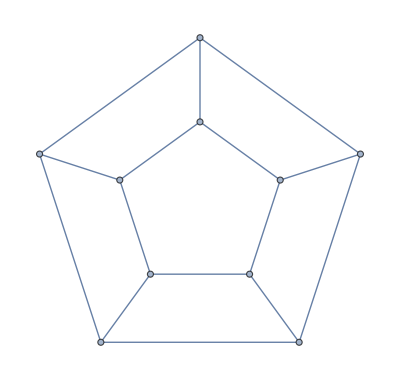

```mathematica
PetersenGraph[5,4]
```